Notebookの場所を指定する

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\ksumiya\Desktop\ReadList_Test

Dataを読み込む
“Number”は, 数として読み込む事を指定(文字として読み込むときは”String”とします), 
“RecordLists”は, datファイル内の行ごとにサブリストとして読み込む(True)事を指定しています. 
Falseにすると全て1行のリストとして読み込みます. 
( 末尾に ; をつけると出力オフになります[計算はされています] )

```mathematica
Data=ReadList["test.dat",Number,RecordLists->True];
Data
```

{{0.,0.,0.},{1.,0.309017,2.},{2.,0.587785,4.},{3.,0.809017,6.},{4.,0.951057,8.},{5.,1.,10.},{6.,0.951057,11.},{7.,0.809017,12.},{8.,0.587785,14.},{9.,0.309017,16.},{10.,0.,20.}}

Dataをキレイに並べて表示する

```mathematica
TableForm[Data]
```

0. | 0. | 0.
1. | 0.309017 | 2.
2. | 0.587785 | 4.
3. | 0.809017 | 6.
4. | 0.951057 | 8.
5. | 1. | 10.
6. | 0.951057 | 11.
7. | 0.809017 | 12.
8. | 0.587785 | 14.
9. | 0.309017 | 16.
10. | 0. | 20.

Dataから行ごとに取り出す

```mathematica
P1=Data⟦1⟧
P2=Data⟦2⟧
```

{0.,0.,0.}

{1.,0.309017,2.}

Esc+[[+Esc で ⟦ になります. “⟦”と”[[“は同じものです. 
( “===”は両辺の真偽を問う関数です. )

```mathematica
Data⟦1⟧ ===Data[[1]]
```

True

Dataから列ごとに取り出す

```mathematica
X=Data⟦All,1⟧
Y=Data⟦All,2⟧
Z=Data⟦All,3⟧
```

{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}

{0.,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,0.}

{0.,2.,4.,6.,8.,10.,11.,12.,14.,16.,20.}

Dataから指定の列たちを好きな順に取り出す

```mathematica
YX=Data⟦All,{2,1}⟧
```

{{0.,0.},{0.309017,1.},{0.587785,2.},{0.809017,3.},{0.951057,4.},{1.,5.},{0.951057,6.},{0.809017,7.},{0.587785,8.},{0.309017,9.},{0.,10.}}

それを点でプロット

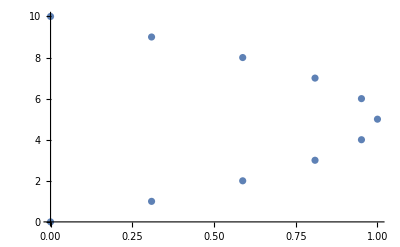

```mathematica
ListPlot[YX]
```

点をつなげてプロット

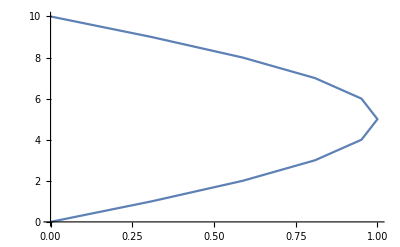

```mathematica
ListPlot[YX,Joined->True]
```

Dataから指定の列たちを1列以上取り出す

```mathematica
XYZ=Data⟦All,1;;3⟧
```

{{0.,0.,0.},{1.,0.309017,2.},{2.,0.587785,4.},{3.,0.809017,6.},{4.,0.951057,8.},{5.,1.,10.},{6.,0.951057,11.},{7.,0.809017,12.},{8.,0.587785,14.},{9.,0.309017,16.},{10.,0.,20.}}

これは元のデータと同じ

```mathematica
Data===XYZ
```

True

Zの値を半分にし, Xと合わせたリストを作ってみる

```mathematica
XHalfZ=Transpose[{X,Z/2}]
```

{{0.,0.},{1.,1.},{2.,2.},{3.,3.},{4.,4.},{5.,5.},{6.,5.5},{7.,6.},{8.,7.},{9.,8.},{10.,10.}}

それをプロット

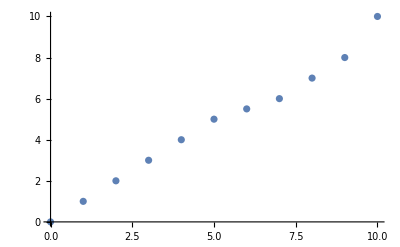

```mathematica
ListPlot[XHalfZ]
```

3次元的にプロットしてみる

```mathematica
ListPointPlot3D[Data]
```

-Graphics3D-

3次元的にプロットしてみる(線でつなぐ)
( ListPointPlot3DにJoinedというoptionはありません. )

```mathematica
Graphics3D[Line[Data],BoxRatios->1,Axes->True]
```

-Graphics3D-

3次元的にプロットしてみる(面で補完する)

```mathematica
ListPlot3D[Data]
```

-Graphics3D-